# 2DEG Magneto-electric Properties

## Inverse scattering time matrix elements

```mathematica
Clear All;
```

Define  constants: (Precision 6 digits)

```mathematica
e = Quantity[(1.602176)*10^(-19),"Coulombs"];
hbar = Quantity[(1.054571)*10^(-34),("Kilograms"*"Meters"^2)/"Seconds"];
me= Quantity[(9.109383)*10^(-31),"Kilograms"];
c = Quantity[(2.997924)*10^(8),"Meters"/"Seconds"];
ϵ0 = Quantity[(8.854187)*10^(-12),("Coulombs"^2*"Seconds"^2)/("Kilograms"*"Meters"^(3))];
```

#### Define system parameters : (Precision 6 digits)

```mathematica
B = Quantity[(1.2),"Kilograms"/("Coulombs"*"Seconds")];
Intensity = Quantity[(2)*10^(6),"Kilograms"/"Seconds"^(3)];
ω = Quantity[(2)*10^(12),"Seconds"^(-1)];
m = 0.071*me;
ω0 = (e*B)/(m);
```

#### Calculate parameters

```mathematica
Efieled  = Sqrt[(2*Intensity)/(c*ϵ0 )];
g = (e*Efieled*((ω0 )^2))/(hbar*ω*((ω0 )^2-(ω)^2));
a = (hbar)/(e*B);
r = Sqrt[(hbar)/(m*ω0)];
```

#### Define functions

Gauss-Hermite functions

```mathematica
χ[x_,N_]:= Exp[-x^2/2]/(√(2^N*N!*√π))HermiteH[N,x];
```

```mathematica
χ2 [x_?NumericQ,N_?NumericQ]:= χ[x,N]*χ[x,N];
```

#### Define inverse scattering matrix

```mathematica
(*ζ [k_]:=N[ NIntegrate[
			(BesselJ[0,g*a*(k-k1)])^2*χ2[a*k2,0]*χ2[a*(k2-k+k1),0]
     ,{k1,Quantity[-100*10^(9),"Meters"^(-1)],Quantity[100*10^(9),"Meters"^(-1)]},{k2,Quantity[-100*10^(9),"Meters"^(-1)],Quantity[100*10^(9),"Meters"^(-1)]}]];*)
```

```mathematica
a
```

5.4851×10^-16 m^2

```mathematica
g
```

5.38756×10^7 per meter

```mathematica
a*g
```

2.95513×10^-8 m

```mathematica
a/r
```

2.34203×10^-8 m

```mathematica
r
```

2.34203×10^-8 m

```mathematica
(*ζ :=N[ NIntegrate[
			(BesselJ[0,2.955*(k-k1)])^2*χ2[2.342*k2,0]*χ2[2.342*(k2-k+k1),0]
     ,{k1,-100,100},{k2,-100,100}]];*)
```

```mathematica
Function Analysis
```

Analysis Function

```mathematica
p1=Plot[χ2 [2.3*(k),1],{k,-π,π},ColorFunction -> (ColorData["RedBlueTones"][Rescale[#2, {0, 1}]] &),
ColorFunctionScaling -> False,PlotRange->{{-π,π},{0,1}},AxesLabel->{Style["k_x",FontSize->20],Style["Λ_00",FontSize->20]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,
PlotLegends->BarLegend["RedBlueTones"]];
Show[p1]
```

-Graphics-

```mathematica
p2=Plot[(BesselJ[0,3*k])^2,{k,-π,π},ColorFunction -> (ColorData["RedBlueTones"][Rescale[#2, {0, 1}]] &),
ColorFunctionScaling -> False,PlotRange->{{-π,π},{0,1}},AxesLabel->{Style["k_x",FontSize->20],Style["Λ_00",FontSize->20]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,
PlotLegends->BarLegend["RedBlueTones"]];
Show[p2]
```

-Graphics-

```mathematica
p3=Plot[(BesselJ[0,3*(k)])^2* χ2 [2.3*(k),0],{k,-π,π},ColorFunction -> (ColorData["RedBlueTones"][Rescale[#2, {0, 1}]] &),
ColorFunctionScaling -> False,PlotRange->{{-π,π},{0,1}},AxesLabel->{Style["k_x",FontSize->20],Style["Λ_00",FontSize->20]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,
PlotLegends->BarLegend["RedBlueTones"]];
Show[p3]
```

-Graphics-

```mathematica
Normalization funtion
```

```mathematica
(*ζ :=N[ NIntegrate[
			χ2[2.342*k2,2]*χ2[2.342*(k2-k+k1),2]
     ,{k1,-100,100},{k2,-100,100}]];*)
```

```mathematica
(*ListPlot[Table[ζ ,{k,-15,15,0.1}]]*)
```

```mathematica
ζ0 :=N[ NIntegrate[
			χ2[2.342*k2,0]*χ2[2.342*(k2-k+k1),0]
     ,{k1,-100,100},{k2,-100,100}]];
```

{0.,4.00133×10^-8,2.65445×10^-8,0.,2.63041×10^-8,0.,1.31638×10^-8,7.11974×10^-9,0.,0.,1.33876×10^-8,0.,1.85971×10^-9,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,7.66706×10^-9,0.,0.,0.,0.0911564,0.,0.,2.15722×10^-8,6.00865×10^-9,0.,6.56069×10^-8,0.,0.,0.,0.,1.70442×10^-8,0.,0.,0.,1.51395×10^-8,4.15402×10^-9,0.,3.65236×10^-9,1.36167×10^-8,3.90559×10^-9,0.,3.65236×10^-9,0.,4.15402×10^-9,1.51395×10^-8,0.,0.,0.,1.70442×10^-8,0.,0.,0.,0.,6.56069×10^-8,0.,6.00865×10^-9,2.15722×10^-8,0.,0.,0.0911564,0.,0.,0.,0.,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,0.0911583,1.27314×10^-8,0.,1.33876×10^-8,0.,0.,7.11974×10^-9,1.31638×10^-8,0.,2.63041×10^-8,0.,2.65445×10^-8,0.,0.}

```mathematica
ζ :=N[ NIntegrate[
			(BesselJ[0,2.955*(k-k1)])^2*χ2[2.342*k2,0]*χ2[2.342*(k2-k+k1),0]
     ,{k1,-100,100},{k2,-100,100}]];
```

{7.73393×10^-9,6.26095×10^-9,0.,0.,0.,0.,1.3496×10^-8,0.,0.,0.,7.01795×10^-9,0.,0.,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.,8.72976×10^-9,0.,1.43211×10^-8,0.,2.15439×10^-8,8.86888×10^-9,2.56127×10^-9,1.84375×10^-8,2.18409×10^-8,9.24813×10^-9,2.19914×10^-8,1.36055×10^-8,0.,8.02084×10^-9,6.29521×10^-10,0.,0.,7.59033×10^-9,0.,9.8253×10^-10,0.,7.1605×10^-9,6.20696×10^-9,0.,0.,6.73463×10^-9,0.,0.,1.06021×10^-8,0.,3.07262×10^-9,0.,1.02766×10^-8,1.3441×10^-8,1.41832×10^-8,0.,9.92151×10^-9,1.36055×10^-8,0.,9.24813×10^-9,2.18409×10^-8,0.,2.56127×10^-9,8.86888×10^-9,2.15439×10^-8,0.,1.43211×10^-8,9.27796×10^-9,2.11927×10^-8,1.40748×10^-8,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,0.0545922,2.14442×10^-9,0.,7.01795×10^-9,0.,0.,0.,1.3496×10^-8,0.,0.054592,0.,1.87755×10^-8,6.26095×10^-9,7.73393×10^-9}

```mathematica
z = {7.733927842866094*^-9,6.2609519757151925*^-9,0.,0.,0.,0.,1.3495995154188115*^-8,0.,0.,0.,7.017951704739299*^-9,0.,0.,0.05459223211165765,0.05459223209327556,0.05459223200900891,0.05459223202404877,0.05459223247033261,0.05459223183686188,0.0545922318777225,0.054592231921598795,0.054592231606224485,0.05459223178093661,0.05459223185523931,0.054592231828717655,0.,8.729757972489052*^-9,0.,1.4321071208184457*^-8,0.,2.1543857671212398*^-8,8.868880819596203*^-9,2.561272055727531*^-9,1.843747330035251*^-8,2.1840909438136233*^-8,9.248130395946373*^-9,2.1991368006255477*^-8,1.3605522217409175*^-8,0.,8.020844460170831*^-9,6.29520966938977*^-10,0.,0.,7.590326725922183*^-9,0.,9.825301485846453*^-10,0.,7.160495488331302*^-9,6.2069621602482004*^-9,0.,0.,6.7346270339382716*^-9,0.,0.,1.0602124472953448*^-8,0.,3.072624524784336*^-9,0.,1.0276574531522047*^-8,1.344095808648771*^-8,1.4183197659478358*^-8,0.,9.921512308289896*^-9,1.3605522050074346*^-8,0.,9.248130172340149*^-9,2.184090236229361*^-8,0.,2.5612720532236312*^-9,8.868880820340115*^-9,2.154385767134697*^-8,0.,1.4321071188700932*^-8,9.277960450694036*^-9,2.119270547105454*^-8,1.407478882315308*^-8,0.054592231828717724,0.054592231855239294,0.05459223178093658,0.05459223160622455,0.05459223192159877,0.0545922318777225,0.05459223183686191,0.054592232470332645,0.05459223202404882,0.05459223200900892,0.05459223209327557,0.05459223211165766,2.144417915793296*^-9,0.,7.017951704739299*^-9,0.,0.,0.,1.3495995154188115*^-8,0.,0.05459201877491295,0.,1.8775510882036056*^-8,6.260950199358353*^-9,7.73392784287965*^-9};
Round[z,0.001]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.,0.,0.,0.,0.,0.,0.,0.,0.055,0.,0.,0.,0.}

```mathematica
v = {0.,4.001332130334577*^-8,2.654448928286929*^-8,0.,2.6304110668267425*^-8,0.,1.316378974597073*^-8,7.119742627937778*^-9,0.,0.,1.3387628240345545*^-8,0.,1.8597132447005123*^-9,0.09115829001213623,0.09115829936273706,0.09115829983317622,0.09115830105682818,0.09115830207976035,0.09115829862329856,0.09115830152014776,0.09115830679406456,0.0911583016031498,0.09115829984212483,0.09115830052544194,0.09115829093002072,0.09115828407937407,7.66705688290641*^-9,0.,0.,0.,0.09115642499924047,0.,0.,2.157222425494006*^-8,6.008650707865361*^-9,0.,6.560689580286843*^-8,0.,0.,0.,0.,1.7044210860740433*^-8,0.,0.,0.,1.513952319749715*^-8,4.154024348456031*^-9,0.,3.6523586523384193*^-9,1.3616667228154247*^-8,3.905590689951684*^-9,0.,3.652358651239777*^-9,0.,4.154024329121772*^-9,1.5139523197497142*^-8,0.,0.,0.,1.7044210960811605*^-8,0.,0.,0.,0.,6.560689580286767*^-8,0.,6.008650707733254*^-9,2.157222425450639*^-8,0.,0.,0.0911564249992405,0.,0.,0.,0.,0.09115828407937407,0.09115829093002072,0.09115830052544195,0.09115829984212485,0.09115830160314976,0.09115830679406461,0.09115830152014776,0.09115829862329865,0.09115830207976026,0.09115830105682814,0.09115829983317619,0.09115829936273706,0.09115829001213617,1.2731378655185869*^-8,0.,1.3387628240345545*^-8,0.,0.,7.119742650522747*^-9,1.3163789745970733*^-8,0.,2.630411066879952*^-8,0.,2.654448928263512*^-8,0.,0.};
Round[v,0.001]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.,0.,0.,0.,0.091,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.091,0.,0.,0.,0.,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.091,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
q1= Round[z,0.001];
q2= Round[v,0.001];
```

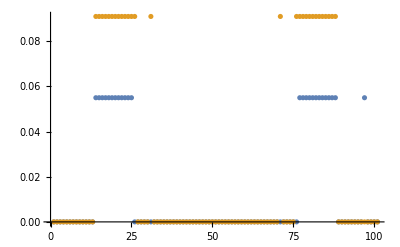

```mathematica
ListPlot[{q1,q2}]
```

#### Testing

```mathematica
ζt :=N[ NIntegrate[
			(BesselJ[0,2.955*(k-k1)])^2*χ2[2.342*k2,0]*χ2[2.342*(k2-k+k1),0]
     ,{k1,-5000,5000},{k2,-5000,5000}]];
```

```mathematica
q3 = Table[ζt ,{k,-5,5,0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in k1 near {k1,k2} = {-16.4795,4220.62}. NIntegrate obtained 8.75812×10^-47 and 8.75812×10^-47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in k1 near {k1,k2} = {-16.2888,4220.62}. NIntegrate obtained 8.75812×10^-47 and 8.75812×10^-47 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in k1 near {k1,k2} = {-16.1743,4220.62}. NIntegrate obtained 8.75812×10^-47 and 8.75812×10^-47 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::inumexpr: Expression {{0.,0,0},{0,0.,0},{0,0,0}} derived from integrand BesselJ[0,2.955 (0.-k1)]^2 χ2[2.342 k2,0] χ2[2.342 (0.+k1+k2),0] is not numerical at {k1,k2} = {0.,-4957.83}.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{0.,8.75812×10^-47,0.,8.75812×10^-47,8.75812×10^-47,0.,0.,8.75812×10^-47,8.75812×10^-47,0.,0.,0.,0.,1.21903×10^-14,0.,4.16725×10^-14,-4.7814×10^-14,0.,0.,1.36226×10^-13,-2.73252×10^-14,3.31761×10^-15,4.89054×10^-14,0.,9.09495×10^-13,0.,0.,0.,0.,0.,0.,-8.59364×10^-15,1.2217×10^-14,2.61978×10^-14,0.,0.,0.,5.37064×10^-14,0.,4.8974×10^-14,0.,0.,4.62104×10^-14,-5.15754×10^-14,0.,1.10376×10^-14,0.,1.14791×10^-14,-6.65794×10^-14,0.,0.,0.,-6.65066×10^-14,1.15075×10^-14,0.,1.10376×10^-14,4.38364×10^-14,-5.16309×10^-14,3.37799×10^-14,0.,0.,4.89594×10^-14,0.,5.34885×10^-14,0.,0.,0.,1.36026×10^-14,-5.1085×10^-15,-5.54875×10^-14,0.,0.,0.,0.,0.,0.,9.09495×10^-13,0.,4.89054×10^-14,3.31761×10^-15,-2.61959×10^-14,1.36232×10^-13,0.,0.,-4.77171×10^-14,4.16725×10^-14,0.,0.,0.,1.6029×10^-15,0.,0.,8.75812×10^-47,8.75812×10^-47,8.75812×10^-47,8.75812×10^-47,8.75812×10^-47,8.75812×10^-47,0.,8.75812×10^-47,0.}

```mathematica
ζt0 :=N[ NIntegrate[
			χ2[2.342*k2,0]*χ2[2.342*(k2-k+k1),0]
     ,{k1,-1000,1000},{k2,-1000,1000}]];
```

```mathematica
q4 = Table[ζt0 ,{k,-5,5,0.1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}